## Alpha-Spektroskopie

### Imports

```mathematica
Filenames = {"AIR", "AMSPKTR","CALIBR"};
Filepaths=NotebookDirectory[]<>"..\\data\\"<>#1&/@Filenames;

rawData = Import[#1<>".DAT","List"] &/@Filepaths ;
kalibrData = rawData[[3]];
airData=rawData[[1]];
sptrData=rawData[[2]];
```

### Energie-Kalibration

{ | Estimate | Standard Error | t-Statistic | P-Value
μ | 33.6787 | 0.128487 | 262.118 | 8.97527254663×10^-939
σ | 1.30333 | 0.128489 | 10.1435 | 4.22007×10^-23
k | 22906.6 | 1955.69 | 11.7128 | 8.04371×10^-30, | Estimate | Standard Error | t-Statistic | P-Value
μ | 138.253 | 0.113263 | 1220.64 | 8.88241422653×10^-1618
σ | 1.27434 | 0.113263 | 11.2512 | 9.10901×10^-28
k | 24651.9 | 1897.51 | 12.9917 | 7.94103×10^-36, | Estimate | Standard Error | t-Statistic | P-Value
μ | 452.902 | 0.129501 | 3497.3 | 2.16471935097×10^-2084
σ | 1.26956 | 0.129494 | 9.80396 | 9.5217×10^-22
k | 21971.7 | 1940.92 | 11.3203 | 4.528×10^-28, | Estimate | Standard Error | t-Statistic | P-Value
μ | 968.743 | 0.0495681 | 19543.7 | 2.43448612328×10^-2847
σ | 1.06534 | 0.0495747 | 21.4897 | 8.29052×10^-85
k | 34850.7 | 1404.34 | 24.8164 | 9.21397×10^-107}

{7011.605764712136/E^(0.29434965581444056*(-33.67872074878762 + x)^2),7717.455825318301/E^(0.30789071693589276*(-138.25335222258695 + x)^2),6904.329823546912/E^(0.31021660410784563*(-452.90210260199433 + x)^2),13050.635733856781/E^(0.4405445287921415*(-968.7432082800937 + x)^2)}

357.4458819940879 + 5.294028183565216*x

nlm["SinglePredictionBands", ConfidenceLevel -> 0.95]

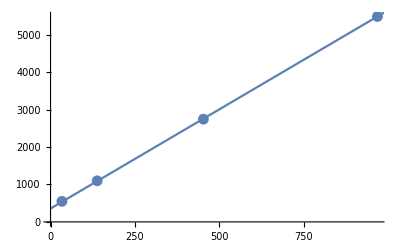

```mathematica
kalibrDampening={10,5,2,1};
kalibrPeakPositions={34,138,452,968};
model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));

kalibrFits=NonlinearModelFit[kalibrData, model[x], {{μ, #1}, {σ, 2}, {k, 8000}}, x]&/@kalibrPeakPositions;


kalibrParameters=#1[[1,1]]&/@(#1[[{1,2}]]&/@#1["ParameterTableEntries"]&/@kalibrFits);

kalibrParameters=MapThread[{#1,#2}&,{kalibrParameters,5486/#1&/@kalibrDampening}];
kalibrParametersLatex=MapThread[Join[#1,{Max[(#1[[2]])/20*(#2-1),1]}]&,{kalibrParameters,kalibrDampening}];
errors=kalibrParametersLatex[[All,3]];
kalibrFunction=NonlinearModelFit[kalibrParameters,a x+b,{a,b},{x},Weights->1/errors^2];

kalibrFitFunctions=Normal/@kalibrFits;

bands95[x_]= nlm["SinglePredictionBands",ConfidenceLevel->0.95];
Export[Filepaths[[3]] <>"-fitted.DAT", N[kalibrParametersLatex], "Table"];



#1["ParameterTable"]&/@kalibrFits
Format[#1,InputForm]&/@kalibrFitFunctions

Format[Normal[kalibrFunction],InputForm]
Format[bands95[x],InputForm]
Show[ListPlot[kalibrParameters],Plot[{Normal[kalibrFunction],bands95[x]},{x,0,1000}]]
```

### Alpha-Peaks von Amerikanum

Null

Null

Null

«1 more identical outputs»

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

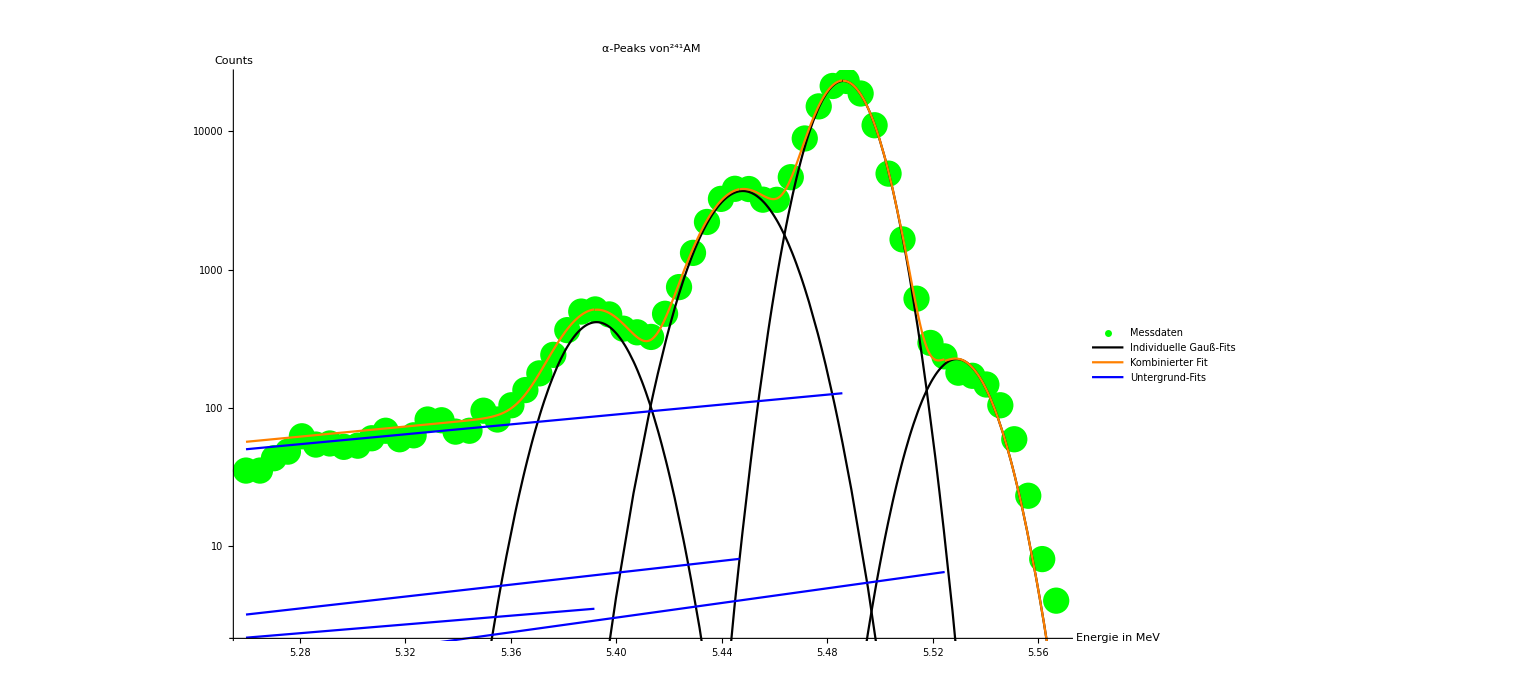

Placed[LineLegend[{1,2,3,4,5},LabelStyle→{-Graphics-,Bold,18},LegendLabel→BesselJ[n,x],LegendLayout→{Row,2}],{0.75,0.25}]

```mathematica
(*Offset als variable, damit der bereich vor den eigentlichen peaks leichter verkleinert/vergrößert werden kann *)
offset=14;
relevantSptrData=Take[MapIndexed[{(Normal[kalibrFunction]/.x->First[#2])/1000,#1}&,sptrData],{940-offset,985}];
(*Models for the gaussian and background fits*)
gaussModel[μ_,σ_,k_,x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));
model2[x_] =a*Exp[b x];

(*Intervals of relevant data for the gaussian fits*)
intervals={{8,14},{17,24},{26,36},{37,43}} + offset;

(*Interval for the background fit(s?)*)
(*
spktrDataIntervals = Take[relevantSptrData,{#1[[1]],#1[[2]]}]&/@intervals;


(*Preliminary fits for the Gaussians*)
spktrBackgroundFit=NonlinearModelFit[Take[relevantSptrData,7+offset], model2[x], {a, b}, x]
spktrPeakFits=NonlinearModelFit[#1, model[x], {{μ, Mean[#1[[All,1]]]}, {σ, 1.86}, {k,Mean[#1[[All,2]]]}}, x]&/@spktrDataIntervals;


(*Refine the fits by fitting it as a sum of gaussians with previously obtained fit values as starting parameters*)
sumGaussParameters={Subscript[μ, #1],Subscript[σ, #1],Subscript[k, #1]}&/@Range[1,4];
sumGaussParameterGuesses=MapThread[{#1,#2[[All,2]]}&,{sumGaussParameters,#1["BestFitParameters"]&/@spktrPeakFits}];
sumGaussParameterGuesses=Flatten[sumGaussParameterGuesses=Transpose[#1]&/@sumGaussParameterGuesses,1]
sumGaussModel[x_]=Total[gaussModel[#1[[1]],#1[[2]],#1[[3]],x]&/@sumGaussParameters]

(*spktrPeakFitsRefined=NonlinearModelFit[relevantSptrData, sumGaussModel[x],sumGaussParameterGuesses, x];*)
spktrPeakFitsRefined["ParameterTable"]


(*Display Parameter Table & Interval for use in LaTeX*)
#1["ParameterTable"]&/@spktrPeakFits
#1["BestFitParameters"]&/@spktrPeakFits
{First[relevantSptrData][[1]],Last[relevantSptrData][[1]]}

(*Export calibrated & cut data, so we don't have to do the same again with PGFplots*)
Export[Filepaths[[2]] <>"-calibrated.DAT", N[relevantSptrData], "Table"];

spktrPeakFits=spktrPeakFits//Normal;

Show[
ListLogPlot[relevantSptrData,PlotRange->All],
ListLogPlot[Flatten[spktrDataIntervals,1],PlotStyle->Red],
LogPlot[Total[spktrPeakFits],{x,First[relevantSptrData][[1]],Last[relevantSptrData][[1]]},PlotStyle->Green],
LogPlot[spktrPeakFits,{x,First[relevantSptrData][[1]],Last[relevantSptrData][[1]]},PlotStyle->Orange],
LogPlot[spktrPeakFitsRefined["BestFit"],{x,First[relevantSptrData][[1]],Last[relevantSptrData][[1]]},PlotStyle->Black],
LogPlot[spktrBackgroundFit["BestFit"],{x,First[relevantSptrData][[1]],Last[relevantSptrData][[1]]},PlotStyle->Black]
]
*)


Module[{bgFitsComplete,fits,bgFits,gaussFits,sortedIntervals,currentInterval,data,noBgData,noGaussData,peakOrder,backgroundFit,gaussFit,i,n,cutoff,piecewise,sumGaussParameters,sumGaussParameterGuesses,sumGaussModel,spktrPeakFitsRefined,cutoffN},
data=relevantSptrData;
bgFitsComplete=bgFits=gaussFits={};
peakOrder={3,2,1,4};
For[i=1,i≤4,i++,
n=peakOrder[[i]];
(*Fit exponential functionto background, so we can remove it from our further calcualtions*)
backgroundFit=Quiet@NonlinearModelFit[Take[data,5+offset], model2[x], {a, b}, x];
(*Define background function until the peak*)

(*Interval relevant to the current peak*)
currentInterval = Take[data,{intervals[[n,1]],intervals[[n,2]]}];
(*Fit gaussian to current peak*)
gaussFit=NonlinearModelFit[currentInterval, model[x], {{μ, Mean[currentInterval[[All,1]]]}, {σ, 1.86}, {k,Mean[currentInterval[[All,2]]]}}, x];
cutoff=gaussFit["BestFitParameters"][[1,2]];
piecewise=Piecewise[{{backgroundFit["BestFit"],x<cutoff},{0,x>cutoff+1}}];
(*Subtrat background from data up to the relevant peak, make sure values stay at 0 or above*)
noBgData={#1[[1]],#1[[2]]-piecewise/.x->#1[[1]]}&/@data;
noBgData={#1[[1]],Max[#1[[2]],0]}&/@noBgData;

(*Subtract Gaussian from data*)
noGaussData={#1[[1]],#1[[2]]-gaussFit["BestFit"]/.x->#1[[1]]}&/@noBgData;
noGaussData={#1[[1]],Max[#1[[2]],0]}&/@noGaussData;
bgFitsComplete=Append[bgFitsComplete,backgroundFit];
bgFits=Append[bgFits,piecewise];
gaussFits=Append[gaussFits,gaussFit];
fits=Join[bgFits,gaussFits];

Print[Show[
ListLogPlot[data,PlotRange->All,PlotStyle->Green],
ListLogPlot[noBgData,PlotRange->All,PlotStyle->Blue],
ListLogPlot[noGaussData,PlotRange->All,PlotStyle->Orange],
LogPlot[piecewise,{x,First[data][[1]],Last[data][[1]]},PlotStyle->Orange],
LogPlot[gaussFit["BestFit"],{x,First[data][[1]],Last[data][[1]]},PlotStyle->Black]
];];
data=noGaussData;
];
fits=Normal[#1]&/@fits;

sumGaussParameters={Subscript[μ, #1],Subscript[σ, #1],Subscript[k, #1]}&/@Range[1,4];
sumGaussParameterGuesses=MapThread[{#1,#2[[All,2]]}&,{sumGaussParameters,#1["BestFitParameters"]&/@gaussFits}];
sumGaussParameterGuesses=Flatten[sumGaussParameterGuesses=Transpose[#1]&/@sumGaussParameterGuesses,1];
sumGaussModel[x_]=Total[gaussModel[#1[[1]],#1[[2]],#1[[3]],x]&/@sumGaussParameters]+Total[bgFits];

spktrPeakFitsRefined=NonlinearModelFit[relevantSptrData, sumGaussModel[x],sumGaussParameterGuesses, x];
finalFits=spktrPeakFitsRefined;
sperateFits=Normal[spktrPeakFitsRefined];
sperateFits=sperateFits[[#1]]&/@Range[1,4];
Print[Show[
ListLogPlot[relevantSptrData,PlotRange->All,PlotStyle->Green,
PlotLegends->Placed[{"Messdaten"},{0.15,0.95}]],
LogPlot[sperateFits,{x,First[data][[1]],Last[data][[1]]},PlotStyle->Black,
PlotLegends->Placed[{"Individuelle Gauß-Fits"},{0.15,0.9}]],
LogPlot[Normal[spktrPeakFitsRefined],{x,First[data][[1]],Last[data][[1]]},PlotStyle->Orange,
PlotLegends->Placed[{"Kombinierter Fit"},{0.15,0.85}]],
LogPlot[bgFits,{x,First[data][[1]],Last[data][[1]]},PlotStyle->Blue,
PlotLegends->Placed[{"Untergrund-Fits"},{0.15,0.80}]],
PlotLabel->"α-Peaks von^241AM",
AxesLabel->{"Energie in MeV","Counts"}
]];
]


Placed[LineLegend[Range[1,5],LabelStyle->{GrayLevel[0.3],Bold,18},LegendLabel->BesselJ[n,x],LegendLayout->{"Row",2}],{0.75,0.25}]
```

```mathematica
,
```